# Numerical solution for the n-pendulum

## Author: Ryan Rubenzahl (12/10/2016)

```mathematica
n=3;
```

```mathematica
Do[lengths[i]=1,{i,1,n}];
Do[masses[i]=1,{i,1,n}];
Do[angles[i][t_]=q[i][t],{i,1,n}];
Do[angledots[i][t_]=q[i]'[t],{i,1,n}];
```

```mathematica
Do[{initialangles[i]:=π/2},{i,n}]
BC = {Table[angles[i][0]==initialangles[i],{i,1,n}],Table[angledots[i][0]==0,{i,1,n}]};
```

```mathematica
T:=1/2 Sum[masses[i]*((Sum[lengths[j]*angledots[j][t]*Cos[angles[j][t]],{j,1,i}])^2+(Sum[lengths[j]*angledots[j][t]*Sin[angles[j][t]],{j,1,i}])^2),{i,1,n}]
U:=-g*Sum[Sum[masses[i]*lengths[j]*Cos[angles[j][t]],{j,1,i}],{i,1,n}]
lagrangian:=T-U
```

```mathematica
Needs["VariationalMethods`"]
ELequations=EulerEquations[lagrangian,Table[angles[i][t],{i,1,n}],t]
```

{-29.43 Sin[q[1][t]]-2. Sin[q[1][t]-q[2][t]] (q[2]'[t])^2-1. Sin[q[1][t]-q[3][t]] (q[3]'[t])^2-3. q[1]''[t]-2. Cos[q[1][t]-q[2][t]] q[2]''[t]-1. Cos[q[1][t]-q[3][t]] q[3]''[t]==0,-19.62 Sin[q[2][t]]+2. Sin[q[1][t]-q[2][t]] (q[1]'[t])^2-1. Sin[q[2][t]-q[3][t]] (q[3]'[t])^2-2. Cos[q[1][t]-q[2][t]] q[1]''[t]-2. q[2]''[t]-1. Cos[q[2][t]-q[3][t]] q[3]''[t]==0,-9.81 Sin[q[3][t]]+1. Sin[q[1][t]-q[3][t]] (q[1]'[t])^2+1. Sin[q[2][t]-q[3][t]] (q[2]'[t])^2-1. Cos[q[1][t]-q[3][t]] q[1]''[t]-1. Cos[q[2][t]-q[3][t]] q[2]''[t]-1. q[3]''[t]==0}

```mathematica
g=9.81;
sol=NDSolve[{ELequations,BC},Table[angles[i][t],{i,1,n}],{t,0,100},Method->{"EquationSimplification"->"Residual"}]
```

{{q[1][t]→InterpolatingFunction[{{0., 100.}}, <>][t],q[2][t]→InterpolatingFunction[{{0., 100.}}, <>][t],q[3][t]→InterpolatingFunction[{{0., 100.}}, <>][t]}}

```mathematica
Do[thetas[i][t_]:=Evaluate[angles[i][t]/.sol][[1]],{i,n}]
Do[xpos[j][t_]:=Evaluate[Sum[lengths[i]*Sin[thetas[i][t]],{i,1,j}]],{j,1,n}]
Do[ypos[j][t_]:=Evaluate[Sum[lengths[i]*Cos[thetas[i][t]],{i,1,j}]],{j,1,n}]
Do[lines[i][t_]:=Evaluate[Line[{{xpos[i][t],-ypos[i][t]},{xpos[i+1][t],-ypos[i+1][t]}}]],{i,1,n-1}]
Do[bobs[i][t_]:=Evaluate[Disk[{xpos[i][t],-ypos[i][t]},0.1]],{i,1,n}]
```

```mathematica
TotalLength=Sum[lengths[i],{i,1,n}];
TotalLength=TotalLength+TotalLength/10;
Animate[Plot[{0},{x,-TotalLength,TotalLength},PlotRange->{-TotalLength,TotalLength},Ticks->None,Epilog->{Line[{{0,0},{xpos[1][t],-ypos[1][t]}}],Table[lines[i][t],{i,1,n-1}],Table[bobs[i][t],{i,1,n}]}, AspectRatio->1],{t,0,100,AnimationRate->1,Appearance->"Open",AnimationRunning->False}]
```

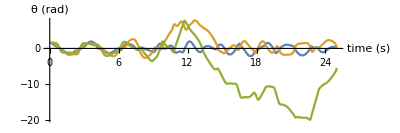

```mathematica
Plot[Evaluate[Table[thetas[i][t],{i,1,n}]],{t,0,25},AxesLabel->{"time (s)","θ (rad)"},PlotLegends->{"θ_1","θ_2","θ_3","θ_4","θ_5","θ_6","θ_7","θ_8","θ_9","θ_10"},AspectRatio->1/3,PlotRange->All]
```